```mathematica
filename="E:\\Research_Tool\\My_Project\\data_process\\9cell7\\20231220_28.csv";afirst=Import[filename];
a=Table[afirst[[i]],{i,1,Length[afirst]}];
ax=Table[a[[i,1]],{i,1,Length[a]}];ay=Table[a[[i,2]],{i,1,Length[a]}];minay=Min[ay];ay=ay-minay;
Fay=Fourier[ay];
Min[ay]-Max[ay]
```

-5.986

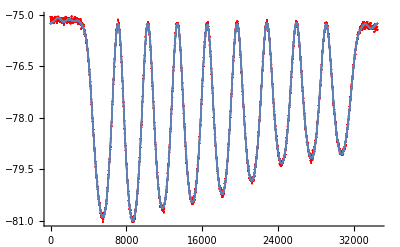

```mathematica
PFay=Table[If[Abs[Fay[[i]]]<2,0,Fay[[i]]],{i,1,Length[a]}];ListPlot[Abs[PFay]];ListFlatteny=Abs[InverseFourier[PFay]];ListFlatten=Table[{ax[[i]],ListFlatteny[[i]]+minay},{i,1,Length[a]}];Show[ListPlot[afirst,PlotStyle->Red],ListPlot[ListFlatten],ImageSize->Full]
```

```mathematica
Export["E:\\Research_Tool\\My_Project\\data_process\\9cell7\\20231220_28_Fourier_filter_data.csv",ListFlatten]
```

E:\Research_Tool\My_Project\data_process\9cell7\20231220_28_Fourier_filter_data.csv

```mathematica
listvalley=Table[If[ListFlatten[[i,2]]>0,j=0,j=ListFlatten[[i,2]]];{ListFlatten[[i,1]],j},{i,1,Length[ListFlatten]}];listvalley2={};
```

```mathematica
For[i=1,i≤Length[ListFlatten],i++,If[(ListFlatten[[i,2]]-ListFlatten[[i+1,2]])*(ListFlatten[[i+1,2]]-ListFlatten[[i+2,2]])<0,Print[{ListFlatten[[i+1,1]],ListFlatten[[i+1,2]]}]]];
```

{314.,-94.0378}

{747.,-94.0786}

{1177.,-94.0434}

{1865.,-94.1358}

{1980.,-94.1349}

{4786.,-105.086}

{6375.,-95.0657}

{7991.,-105.119}

{9541.,-95.0915}

{11163.,-105.249}

{12693.,-95.1789}

{14319.,-105.697}

{15880.,-95.2075}

{17477.,-105.685}

{19028.,-95.1768}

{20636.,-105.643}

{22192.,-95.2516}

{23794.,-105.505}

{25351.,-95.2906}

{26952.,-105.669}

{28498.,-95.2356}

{30158.,-105.38}

{32917.,-94.2925}

{33119.,-94.297}

{34539.,-94.1654}

{35080.,-94.2513}

Part::partw: {{0.,-94.1147},{0.,-94.1145},{0.,-94.1143},{3.,-94.114},{4.,-94.1138},{5.,-94.1136},{5.,-94.1134},{5.,-94.1132},{6.,-94.113},{6.,-94.1128},«74839»} 的部分 74850 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
width=1000
```

1000

```mathematica
listvalley2=Table[listvalley[[1+i*width;;width+i*width]],{i,0,Length[listvalley]/1000-1}]
```

{{{0.,-94.1147},{0.,-94.1145},{0.,-94.1143},{3.,-94.114},{4.,-94.1138},{5.,-94.1136},{5.,-94.1134},{5.,-94.1132},{6.,-94.113},982,{463.,-94.05},{464.,-94.0501},{464.,-94.0501},{464.,-94.0502},{465.,-94.0502},{465.,-94.0503},{465.,-94.0504},{466.,-94.0504},{466.,-94.0505}},72,{1}}
 |  |  |  |

```mathematica
listvalley3=Sort[Table[Sort[listvalley2[[i]],#1[[2]]<#2[[2]]&][[1]],{i,1,Length[listvalley]/1000}],#1[[2]]<#2[[2]]&]
```

{{14319.,-105.697},{17477.,-105.685},{26952.,-105.669},{26994.,-105.654},{17552.,-105.649},{20636.,-105.643},{14230.,-105.639},{23794.,-105.505},{23660.,-105.389},{30158.,-105.38},{20833.,-105.375},{11163.,-105.249},{30365.,-105.148},{20365.,-105.135},{7991.,-105.119},{7997.,-105.118},{4786.,-105.086},{4683.,-105.022},{11350.,-105.012},{29886.,-104.941},{24125.,-104.78},{10872.,-104.671},{17086.,-104.643},{14709.,-104.626},{26523.,-104.413},{5143.,-104.272},{7527.,-103.794},{27473.,-103.776},{18015.,-103.629},{8474.,-103.58},{13752.,-103.54},{4216.,-103.399},{23195.,-103.06},{30836.,-102.952},{21304.,-102.53},{11831.,-102.069},{19894.,-101.99},{29401.,-101.945},{10391.,-101.522},{24599.,-101.178},{16610.,-100.844},{5618.,-100.736},{15189.,-100.471},{26033.,-100.262},{3743.,-100.063},{7041.,-99.8192},{8955.,-99.1608},{31328.,-99.1291},{13267.,-98.9923},{27953.,-98.9544},{18487.,-98.857},{22719.,-98.4515},{21774.,-97.5595},{28901.,-97.2972},{19419.,-97.2392},{12303.,-97.1176},{9908.,-96.8446},{3265.,-96.5347},{25068.,-96.3334},{16138.,-96.1865},{6092.,-96.1518},{31811.,-96.116},{2798.,-94.773},{32283.,-94.7617},{32765.,-94.3073},{33239.,-94.2919},{35080.,-94.2513},{33708.,-94.2312},{2336.,-94.2145},{34173.,-94.2109},{1865.,-94.1358},{0.,-94.1147},{747.,-94.0786},{1408.,-94.0689}}

```mathematica
listvalley4={{14237,-3.4278920235959354},{4681,-3.253997541035841},{20555,-3.202357776449174},{7897,-3.1018472786100384},{17417,-3.085382029029094},{8000,-3.0436194337848685},{13999,-3.041291738514238},{11049,-2.845461606512293},{26871,-2.841807594772721},{10999,-2.829898790475027},{27000,-2.7253937885145456},{5000,-2.6726575923318903},{23735,-2.5723449371276215},{30081,-2.5298994591381367},{29999,-2.4921672827350174},{24000,-2.1344896949958105},{16999,-1.942183406522854},{21000,-1.7661122346002942}}
```

{{14237,-3.42789},{4681,-3.254},{20555,-3.20236},{7897,-3.10185},{17417,-3.08538},{8000,-3.04362},{13999,-3.04129},{11049,-2.84546},{26871,-2.84181},{10999,-2.8299},{27000,-2.72539},{5000,-2.67266},{23735,-2.57234},{30081,-2.5299},{29999,-2.49217},{24000,-2.13449},{16999,-1.94218},{21000,-1.76611}}

```mathematica
listvalley5=Sort[listvalley4]
```

{{4681,-3.254},{5000,-2.67266},{7897,-3.10185},{8000,-3.04362},{10999,-2.8299},{11049,-2.84546},{13999,-3.04129},{14237,-3.42789},{16999,-1.94218},{17417,-3.08538},{20555,-3.20236},{21000,-1.76611},{23735,-2.57234},{24000,-2.13449},{26871,-2.84181},{27000,-2.72539},{29999,-2.49217},{30081,-2.5299}}

```mathematica
listvalley6={{4681,-3.253997541035841},{7897,-3.1018472786100384},{11049,-2.845461606512293},{14237,-3.4278920235959354},{17417,-3.085382029029094},{20555,-3.202357776449174},{23735,-2.5723449371276215},{26871,-2.841807594772721},{30081,-2.5298994591381367}}
```

{{4681,-3.254},{7897,-3.10185},{11049,-2.84546},{14237,-3.42789},{17417,-3.08538},{20555,-3.20236},{23735,-2.57234},{26871,-2.84181},{30081,-2.5299}}

```mathematica
Show[Plot[ifun[x],{x,4000,30350}],ListPlot[listvalley6,PlotStyle->Red]]
```

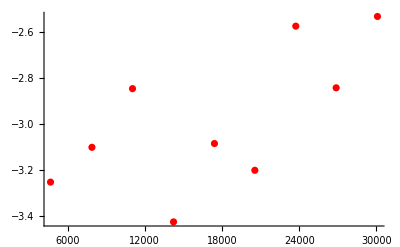

```mathematica
Max[{{1,2},{1,3},{2,4}}]
```